```mathematica
t=Import["D:\\data.txt","Table"];
```

```mathematica
Length[t]
```

10

```mathematica
t=Table[t[[i]],{i,1,Length[t],10}];
t=Take[t,10000]
```

{{0.2,0.},{0.206,0.008},{0.212,0.016},{0.218,0.024},{0.224,0.032},{0.23,0.04},9989,{-0.660865,0.183656},{-0.661733,0.173685},{-0.662601,0.163715},{-0.66347,0.153744},{-0.664338,0.143773}}
 |  |  |  |

```mathematica
Length[t]
```

10000

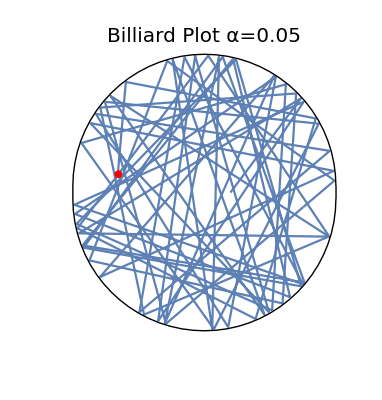

```mathematica
g1=ListPlot[t,PlotRange->All,AxesLabel->{"x","y"},Axes->False]/.Point->Line;
g2=Graphics[{Red,Disk[t[[-1]],0.03]}];
g4=Graphics[{Thick,Black,Circle[{0,0.05},1+0.01,{0,π}],
Thick,Black,Circle[{0,-0.05},1+0.01,{π,2 π}],
Thick,Black,Line[{{1.011,-0.05},{1.011,0.05}}],
Thick,Black,Line[{{-1.01,-0.05},{-1.01,0.05}}]
}];
g3=Graphics[Text[Style["Billiard Plot "<>"α=0.05",20],{0,1.2}]];
Show[g1,g2,g3,g4,PlotRange->{{-1.1,1.1},{-1.1,1.2}},AspectRatio->Automatic]
```

```mathematica
pict={};
Do[
temp=Take[t,i];
g1=ListPlot[temp,PlotRange->All,AxesLabel->{"x","y"},Axes->False]/.Point->Line;
g2=Graphics[{Red,Disk[temp[[-1]],0.03]}];
g4=Graphics[{Thick,Black,Circle[{0,0.05},1+0.01,{0,π}],
Thick,Black,Circle[{0,-0.05},1+0.01,{π,2 π}],
Thick,Black,Line[{{1.011,-0.05},{1.011,0.05}}],
Thick,Black,Line[{{-1.01,-0.05},{-1.01,0.05}}]
}];
g3=Graphics[Text[Style["Billiard Plot "<>"α=0.05",20],{0,1.2}]];
g=Show[g1,g2,g3,g4,PlotRange->{{-1.1,1.1},{-1.1,1.2}},AspectRatio->Automatic];
AppendTo[pict,g];
Print[i,"/",Length[t]],

{i,1,Length[t],Floor[Length[t]/100]}];
Export["C:\\Users\\ChenYangyao\\Desktop\\pic_ch3_lorenz\\mma3d\\a2.gif",pict]
```

1/10000

101/10000

201/10000

301/10000

401/10000

501/10000

601/10000

701/10000

801/10000

901/10000

1001/10000

1101/10000

1201/10000

1301/10000

1401/10000

1501/10000

1601/10000

1701/10000

1801/10000

1901/10000

2001/10000

2101/10000

2201/10000

2301/10000

2401/10000

2501/10000

2601/10000

2701/10000

2801/10000

2901/10000

3001/10000

3101/10000

3201/10000

3301/10000

3401/10000

3501/10000

3601/10000

3701/10000

3801/10000

3901/10000

4001/10000

4101/10000

4201/10000

4301/10000

4401/10000

4501/10000

4601/10000

4701/10000

4801/10000

4901/10000

5001/10000

5101/10000

5201/10000

5301/10000

5401/10000

5501/10000

5601/10000

5701/10000

5801/10000

5901/10000

6001/10000

6101/10000

6201/10000

6301/10000

6401/10000

6501/10000

6601/10000

6701/10000

6801/10000

6901/10000

7001/10000

7101/10000

7201/10000

7301/10000

7401/10000

7501/10000

7601/10000

7701/10000

7801/10000

7901/10000

8001/10000

8101/10000

8201/10000

8301/10000

8401/10000

8501/10000

8601/10000

8701/10000

8801/10000

8901/10000

9001/10000

9101/10000

9201/10000

9301/10000

9401/10000

9501/10000

9601/10000

9701/10000

9801/10000

9901/10000

C:\Users\ChenYangyao\Desktop\pic_ch3_lorenz\mma3d\a2.gif